```mathematica
τc[τcbar_]:=τcbar*Log[1/(1-RandomReal[])]
```

```mathematica
phaseshift[τ_,τcbar_,N_]:=Table[ τc[τcbar]< τ,N]
```

```mathematica
ephiave[t_,τcbar_,N_]:= Mean[Exp[-ⅈ*If[#,2π*RandomReal[{-1,1}],0]&/@phaseshift[t,τcbar,N]]]
```

```mathematica
absephivar[t_,τcbar_,N_]:= Abs[Variance[Exp[-ⅈ*If[#,2π*RandomReal[{-1,1}],0]&/@phaseshift[t,τcbar,N]]]]
```

```mathematica
tmin = 0;
tmax = 5;
tstep = 0.01;
n = 1000;
τcbar = 1;
ephi2=Table[{t,Abs[ephiave[t,τcbar,n]]^2},{t,tmin,tmax,tstep}];
absephivarTable = Table[{t,absephivar[t,τcbar,n]},{t,tmin,tmax,tstep}];
```

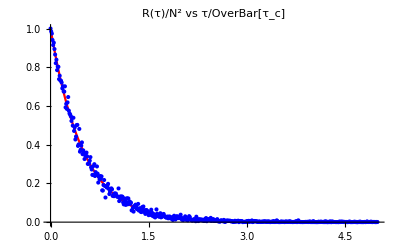

```mathematica
Show[Plot[Exp[-2t/τcbar],{t,tmin,tmax}, PlotStyle-> Red, PlotRange->All, PlotLabel-> "R(τ)/N^2 vs τ/OverBar[τ_c]"],ListPlot[ephi2, PlotStyle-> Blue]]
```

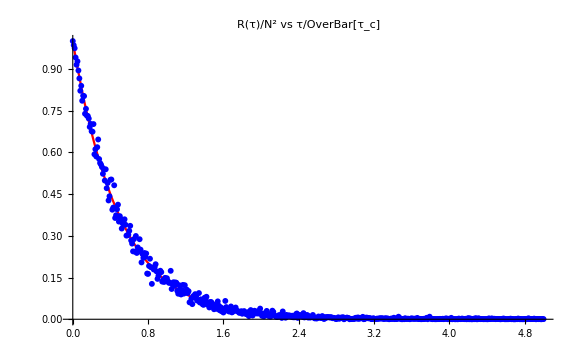

```mathematica
Show[%38,ImageSize->Large]
```

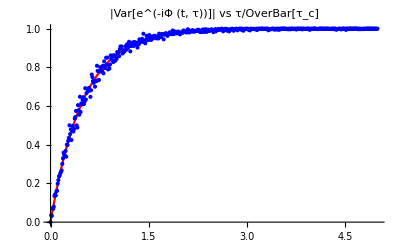

```mathematica
Show[Plot[1-Exp[-2t/τcbar],{t,tmin,tmax}, PlotStyle->Red, PlotRange-> All, PlotLabel-> "|Var[e^(-iΦ (t, τ))]| vs τ/OverBar[τ_c]"],ListPlot[absephivarTable, PlotStyle-> Blue]]
```

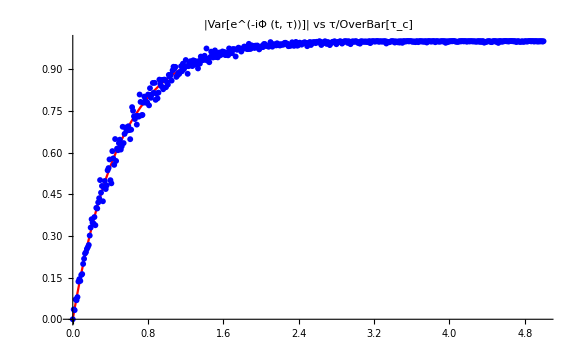

```mathematica
Show[%62,ImageSize->Large]
```